```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Input","Printout"],CellElementSpacings->{"CellMinHeight"->0,"ClosedCellHeight"->0},Background->Hue[.8],CellMargins->-2,CellOpen->False,CellFrame->0,ShowCellBracket->False,ShowCellLabel->False,ShowCellTags->False]}]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
curve1=Import["../data/out/curve1.csv"];
curve2=Import["../data/out/curve2.csv"];
matchings=Table[Import["../data/out/matching"<>ToString[i]<>".csv"],{i,3}];
aStarPoints=Import["../data/out/debug_points.csv"];
debugPointsOld=Import["../data/out/debug_points_old.csv"];
```

```mathematica
ImageNorm=Norm[#,2]^2&;
ParamNorm=Norm[#,Infinity]&;
```

```mathematica
(* Interpolating Line objects: *)
ClearAll[LineInterpolation,LineBreakPoints];

Options[LineBreakPoints]={Normalize->False};
LineBreakPoints[line_,opts:OptionsPattern[]]:=(
accum=Accumulate[#]&@Prepend[Norm[Subtract@@#]&/@Partition[line[[1]],2,1],0];
If[OptionValue[Normalize],accum/ArcLength[line],accum]);

LineInterpolation[line_,opts:OptionsPattern[{LineBreakPoints,Interpolation}]]:=(
breakpoints=LineBreakPoints[line,Sequence@@FilterRules[{opts},Options[LineBreakPoints]]];
Interpolation[Transpose[{breakpoints,line[[1]]}],InterpolationOrder->1,Sequence@@FilterRules[{opts},Options[Interpolation]]]);
```

```mathematica
c1=LineInterpolation[Line[curve1]];
c2=LineInterpolation[Line[curve2]];
ms=LineInterpolation[Line[#],Normalize->True]&/@matchings;
m=ms[[1]];
```

```mathematica
len1=ArcLength@Line[curve1];
len2=ArcLength@Line[curve2];
```

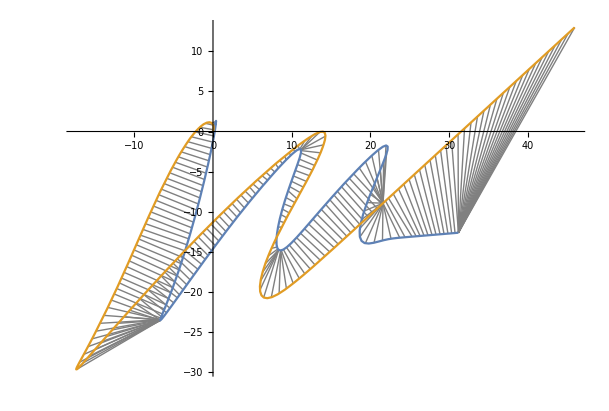

```mathematica
Show[
ListLinePlot[
Table[Quiet@({c1[#1],c2[#2]}&@@m[t]),{t,0,1,1/200}],
PlotStyle->Directive[Gray,Thin]
],
ParametricPlot[{c1[t len1],c2[t len2]},{t,0,1}],
AspectRatio->Automatic
]
```

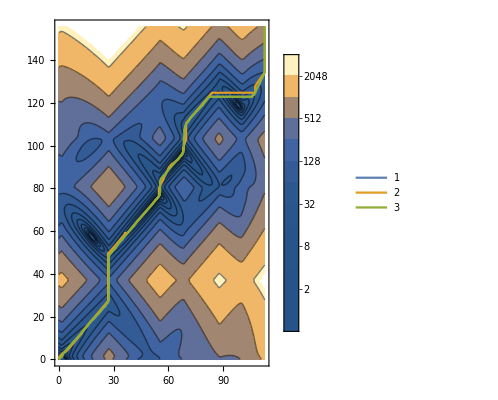

```mathematica
Show[
ContourPlot[
ImageNorm[c1[t1]-c2[t2]],
{t1,0,len1},
{t2,0,len2},
PlotLegends->Automatic,
Contours->Function[{min,max},PowerRange[min+1,max+1,2]]
],
ParametricPlot[
Evaluate[#[t]&/@ms],
{t,0,1},
PlotLegends->Range[Length[ms]]
],
AspectRatio->Automatic
]
```

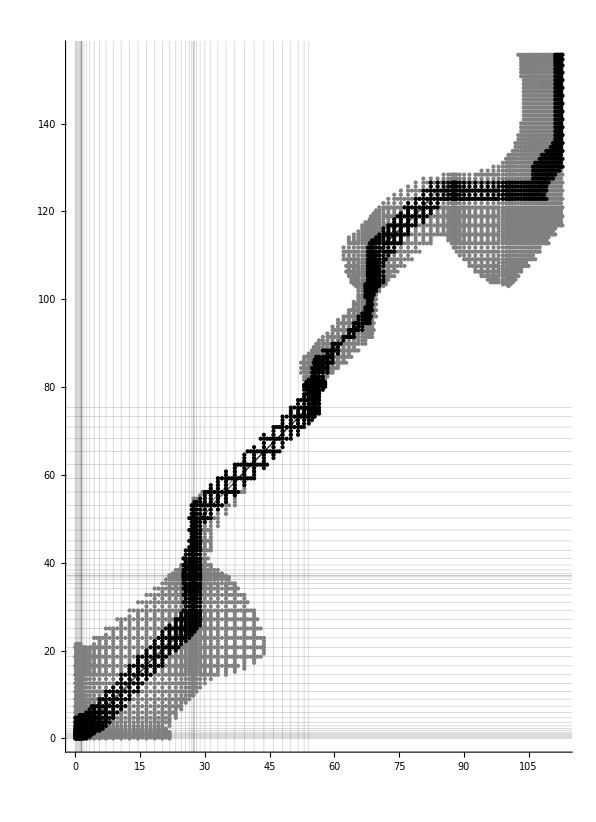

```mathematica
Show[
Graphics[{
Gray,
Point[debugPointsOld]
}],
Graphics[{
(*PointSize[Small],*)
Point[
aStarPoints,
VertexColors->ColorData["DarkRainbow"]/@Rescale[Range[Length[aStarPoints]]]
]
}],
ParametricPlot[
Evaluate[#[t]&/@ms],
{t,0,1},
PlotStyle->Directive[Opacity[0.4],Black,Thick]
],
AspectRatio->Automatic,
Axes->True,
GridLinesStyle->Directive[Opacity[0.2],Black],
GridLines->{
LineBreakPoints[Line[curve1]],
LineBreakPoints[Line[curve2]]
}
]
```

```mathematica
ClearAll[Cost,Dist];
Cost[f_,t_?NumericQ]:=ImageNorm[c1[#1]-c2[#2]]&@@f[t];
Dist[f_,t_?NumericQ]:=ParamNorm[f'[t]];
```

```mathematica
NIntegrate[Cost[#,t]Dist[#,t],{t,0,1},Method->"LocalAdaptive"]&/@ms
```

{13557.8,13738.1,13557.8}